未补偿 β=-4/(Rf^2 (4/Rf^2-(-4/Rf-C1 s) (-2/Rf-1/Rg-Cg s)))

带补偿 β=-(4/Rf^2-Cf s (-4/Rf-C1 s))/(4/Rf^2-(-4/Rf-C1 s) (-2/Rf-1/Rg-Cf s-Cg s))

未补偿 β=(1.6×10^18)/(4.8×10^18+5.6×10^9 s+s^2)

未补偿β的极点(Hz): {-7.2313×10^8,-1.68138×10^8}

Open Loop

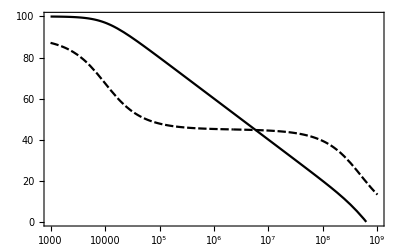

Ideal Loop

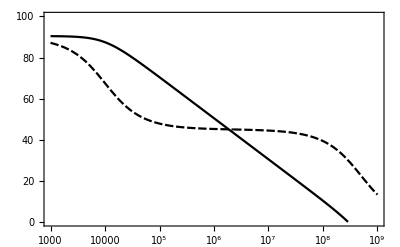

实际环路极点(Hz): {-9999.07}

Real Loop

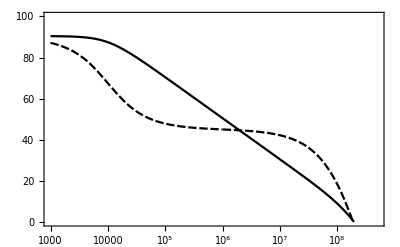

补偿的β=(0.000016+2.8×10^-14 s+7.×10^-24 s^2)/(0.000048+8.4×10^-14 s+1.7×10^-23 s^2)

补偿的β的极点(Hz){{{-6.8146×10^8,-1.04952×10^8}}}

补偿的β的零点(Hz){{{-5.26693×10^8,-1.09927×10^8}}}

Comped Loop

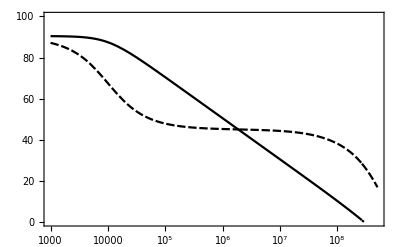

Ideal Close Loop

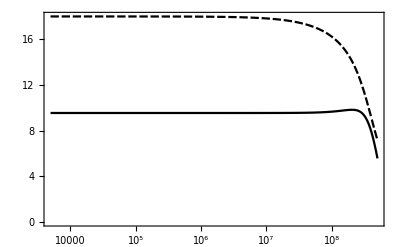

UC Close Loop

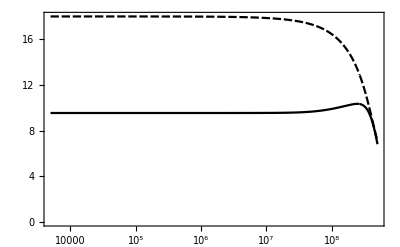

Comped Close Loop

-Graphics-

```mathematica
(**)
mybode=Function[{tf,f0,f1,db0,db1,ph0,ph1},
LogLinearPlot[{
20*Log10[Abs[tf[ⅈ 2π f]]],
(180/π*Arg[tf[ⅈ 2π f]]-ph0)/(ph1-ph0)*(db1-db0)+db0
},{f,f0,f1},PlotRange->{db0,db1},PlotTheme->"Monochrome",GridLines->Automatic,Frame->True
] //Print;
];
(* 分布参数模拟 *)
ClearAll[Rg,Rf,Cg,Cf,C1,s,x,y];
Par[x_,y_]:=(x*y)/(x+y);
sol=Solve[{(0-x)/Rg+(0-x)/(1/(s Cg))+(y-x)/(Rf/2)+(1-x)/(1/(s Cf))==0,
(x-y)/(Rf/2)+(1-y)/(Rf/2)+(0-y)/(1/(s C1))==0
},{x,y}];
x=(x/.sol[[1]][[1]]);
β[ss_]:=x/.s->ss;
Print["未补偿 β=",x/.Cf->0];
Print["带补偿 β=",x];
poles=x/.Solve[1/x==0,s];
(*Print["极点: ", poles];*)
(* 实际未补偿参数 *)
AD0=10^5;p0=2π 10*10^3;p1=2π 500*10^6;
Rg=250;Rf=500;C1=2*10^-12;Cg=5*10^-12;delay=0.1*10^-9;
Cf=0;
Print["未补偿 β=",N[Simplify[x]]];
Print["未补偿β的极点(Hz): ",(s/.NSolve[1/x==0])/(2 π)]
(* 开环增益 *)
AD[s_]:=AD0/((1+s/p0)(1+s/p1));
Print["Open Loop"];
mybode[AD,1000,1000000000,0,100,-180,20]
(* 理想环路增益 *)
AL[s_]:=-AD[s]*Rg/(Rf+Rg);
Print["Ideal Loop"];
mybode[AL,1000,1000000000,0,100,0,200]
(* 实际环路增益 *)
AL1[s_]:=-AD[s]*β[s]*ⅇ^(-s delay);
Print["实际环路极点(Hz): ",(s/.NSolve[1/AL1[s]==0,s])/2/π]
Print["Real Loop"];
mybode[AL1,1000,500000000,0,100,0,200]
(* 补偿环路增益 *)
Cf=3.5*10^-12;
AL2[s_]:=-AD[s]*β[s]*ⅇ^(-s delay);
Print["补偿的β=",Simplify[N[β[s]]]];
Print["补偿的β的极点(Hz)",
N[TransferFunctionPoles[TransferFunctionModel[β[s],s]]/2/π]];
Print["补偿的β的零点(Hz)",
N[TransferFunctionZeros[TransferFunctionModel[β[s],s]]/2/π]];
Print["Comped Loop"];
mybode[AL2,1000,500000000,0,100,0,200]
(* 闭环增益 *)
ACL[s_]:=AD[s]/(1-AL[s]);
ACL1[s_]:=AD[s]/(1-AL1[s]);
ACL2[s_]:=AD[s]/(1-AL2[s]);
Print["Ideal Close Loop"];
mybode[ACL,5000,500000000,0,18,-180,0]
Print["UC Close Loop"];
mybode[ACL1,5000,500000000,0,18,-180,0]
Print["Comped Close Loop"];
mybode[ACL2,5000,500000000,0,18,-180,0]
```

```mathematica
Simplify[N[AL1[s]]]
```

(ⅇ^(-5.×10^-10 s) (2.63189×10^13+123699. s+0.000154624 s^2))/(-2.36871×10^9-37715.4 s-0.000259577 s^2-3.09712×10^-13 s^3-7.35×10^-23 s^4)

```mathematica
Solve[-2.3687050562614455*^9-37715.42032185049 s-0.00025957696057136737 s^2-3.097116781800505*^-13 s^3-7.349999999999999*^-23 s^4==0,s]
```

{{s→-3.14159×10^9},{s→-8.88317×10^8},{s→-1.83792×10^8},{s→-62831.9}}

```mathematica
Solve[1/AL1[s]==0,s]
```

{{}}

```mathematica
Factor[2.4*^17+1.2*^9 s+s^2]
```

1. (2.5359×10^8+1. s) (9.4641×10^8+1. s)

```mathematica
N[AD[s]]
```

100000./((1.+3.1831×10^-10 s) (1.+0.0000159155 s))

```mathematica
(4.*^-6+2.5600000000000003*^-14 s+3.2*^-23 s^2)/(0.000012+8.560000000000001*^-14 s+8.199999999999999*^-23 s^2);
Factor[4.*^-6+2.5600000000000003*^-14 s+3.2*^-23 s^2]
Solve[4.*^-6+2.5600000000000003*^-14 s+3.2*^-23 s^2==0,s]
Factor[0.000012+8.560000000000001*^-14 s+8.199999999999999*^-23 s^2]
Solve[0.000012+8.560000000000001*^-14 s+8.199999999999999*^-23 s^2==0,s]
```

3.2×10^-23 (2.12917×10^8+1. s) (5.87083×10^8+1. s)

{{s→-5.87083×10^8},{s→-2.12917×10^8}}

8.2×10^-23 (1.66857×10^8+1. s) (8.77045×10^8+1. s)

{{s→-8.77045×10^8},{s→-1.66857×10^8}}

```mathematica
(s/.{{s->-5.870828693386973*^8},{s->-2.1291713066130286*^8}})/2/π
(s/.{{s->-8.770450270273836*^8},{s->-1.6685741199700686*^8}})/2/π
```

{-9.34371×10^7,-3.38868×10^7}

{-1.39586×10^8,-2.65562×10^7}